```mathematica
SetDirectory["/home/botingw/git/SensPaper/figs/apBfigs"]
```

/home/botingw/git/SensPaper/figs/apBfigs

```mathematica
FileNames[]
```

{Allexpt_config1.txt,Allexpt_corrdr_hist+1_f0_samept.pdf,Allexpt_corrdr_plotlist_samept.m,Allexpt_corrdr_xQ+1_f0_samept.pdf,Allexpt_corr_hist+1_f0_samept.pdf,Allexpt_corr_plotlist_samept.m,Allexpt_corr_xQ+1_f0_samept.pdf,Allexpt_xQbyexpt_xQ.pdf,CT14H2LHeC_config1.txt,jetnew_corrdr_plotlist_samept.m,jpnew_config1.txt,jpnew_corrdr_xQ+1_f8_samept.pdf,ttbar_config1.txt,ttbar_corrdr_plotlist_samept.m,ttbar_corrdr_xQ+1_f8_samept.pdf,user_func.txt,Zpt_config1.txt,Zpt_corrdr_plotlist_samept.m,Zpt_corrdr_xQ+1_f8_samept.pdf,Zpt_dr_hist+1_samept.pdf,Zpt_dr_plotlist_samept.m}

### Run

#### Zpt δr hist

```mathematica
Zptdrhist=Drop[ReadList[OpenRead["Zpt_dr_plotlist_samept.m"],String ],1]//StringJoin;
```

```mathematica
Zptdrhist//Dimensions
```

{}

```mathematica
Export[
"./test/"<>"Zpt_dr_hist+1_samept.pdf",
ToExpression[StringReplace[Zptdrhist,"NNLOall"->"NNLO"] ][[3]] 
]
```

./test/Zpt_dr_hist+1_samept.pdf

#### Zpt f8 |sens| xQ

```mathematica
ZptsensxQf8=
Get["Zpt_corrdr_plotlist_samept.m"][[8+3,1]](*,
PlotLabel->"S_f(dbar(x,Q),r_i), CT14HERA2NNLO"
*)
```

-Graphics-

```mathematica
Show[
ZptsensxQf8,
PlotLabel->Style["|S_f(sig(H0), 14 TeV, r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"Zpt_corrdr_xQ+1_f8_samept.pdf",
Show[
ZptsensxQf8,
PlotLabel->Style["|S_f(sig(H0), 14 TeV, r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
]
```

./test/Zpt_corrdr_xQ+1_f8_samept.pdf

```mathematica
"b̄"
```

b̄

#### ttbar f8 |sens| xQ

```mathematica
ttbarsensxQf8=
Get["ttbar_corrdr_plotlist_samept.m"][[8+3,1]](*,
PlotLabel->"S_f(dbar(x,Q),r_i), CT14HERA2NNLO"
*)
```

-Graphics-

```mathematica
Show[
ttbarsensxQf8,
PlotLabel->Style["|S_f(sig(H0), 14 TeV, r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"ttbar_corrdr_xQ+1_f8_samept.pdf",
Show[
ttbarsensxQf8,
PlotLabel->Style["|S_f(sig(H0), 14 TeV, r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
]
```

./test/ttbar_corrdr_xQ+1_f8_samept.pdf

#### jpnew f8 |sens| xQ

```mathematica
jpnewsensxQf8=
Get["jpnew_corrdr_plotlist_samept.m"][[8+3,1]]
```

-Graphics-

```mathematica
Show[
jpnewsensxQf8,
PlotLabel->Style["|S_f(sig(H0), 14 TeV, r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"jpnew_corrdr_xQ+1_f8_samept.pdf",
Show[
jpnewsensxQf8,
PlotLabel->Style["|S_f(sig(H0), 14 TeV, r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
]
```

./test/jpnew_corrdr_xQ+1_f8_samept.pdf

#### Allexpt f0 |sens| xQ

```mathematica
AllexptsensxQf0=
Get["Allexpt_corrdr_plotlist_samept.m"][[0+3,1]]
```

-Graphics-

```mathematica
Show[
AllexptsensxQf0,
PlotLabel->Style["|S_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"Allexpt_corrdr_xQ+1_f0_samept.pdf",
Show[
AllexptsensxQf0,
PlotLabel->Style["|S_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
]
```

./test/Allexpt_corrdr_xQ+1_f0_samept.pdf

#### Allexpt f0 |sens| hist

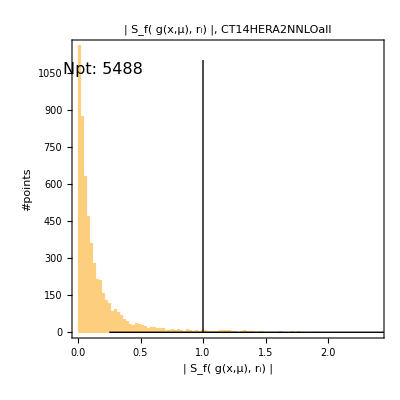

```mathematica
Allexptsenshistf0=
Get["Allexpt_corrdr_plotlist_samept.m"][[0+3,3]]
```

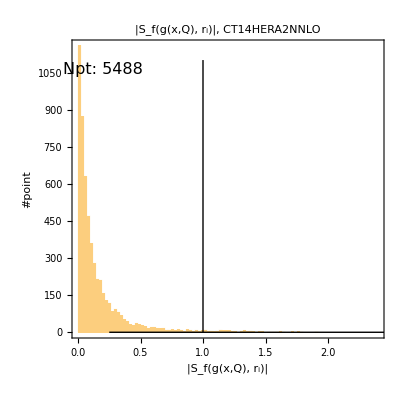

```mathematica
Show[
Allexptsenshistf0,
PlotLabel->Style["|S_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameLabel->{Style["|S_f(g(x,Q), r_i)|",18,Black],Style["#point",18,Black]},
LabelStyle->Black
]
```

```mathematica
Export[
"./test/"<>"Allexpt_corrdr_hist+1_f0_samept.pdf",
Show[
Allexptsenshistf0,
PlotLabel->Style["|S_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameLabel->{Style["|S_f(g(x,Q), r_i)|",18,Black],Style["#point",18,Black]},
LabelStyle->Black
]
]
```

./test/Allexpt_corrdr_hist+1_f0_samept.pdf

#### Allexpt f0 |corr| xQ

```mathematica
AllexptcorrxQf0=
Get["Allexpt_corr_plotlist_samept.m"][[0+3,1]]
```

-Graphics-

```mathematica
Show[
AllexptcorrxQf0,
PlotLabel->Style["|C_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"Allexpt_corr_xQ+1_f0_samept.pdf",
Show[
AllexptcorrxQf0,
PlotLabel->Style["|C_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
]
```

./test/Allexpt_corr_xQ+1_f0_samept.pdf

#### Allexpt f0 |corr| hist

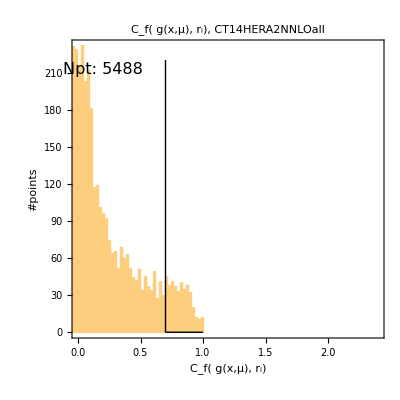

```mathematica
Allexptcorrhistf0=
Get["Allexpt_corr_plotlist_samept.m"][[0+3,3]]
```

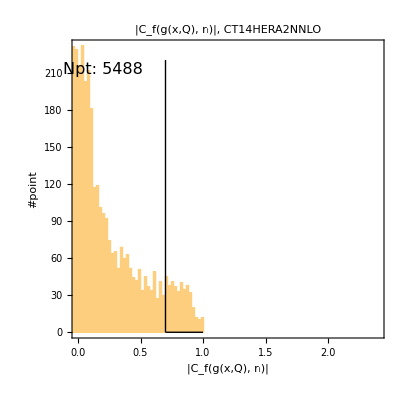

```mathematica
Show[
Allexptcorrhistf0,
PlotLabel->Style["|C_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameLabel->{Style["|C_f(g(x,Q), r_i)|",18,Black],Style["#point",18,Black]},
LabelStyle->Black
]
```

```mathematica
Export[
"./test/"<>"Allexpt_corr_hist+1_f0_samept.pdf",
Show[
Allexptcorrhistf0,
PlotLabel->Style["|C_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameLabel->{Style["|C_f(g(x,Q), r_i)|",18,Black],Style["#point",18,Black]},
LabelStyle->Black
]
]
```

./test/Allexpt_corr_hist+1_f0_samept.pdf

#### xQ plot by expt id

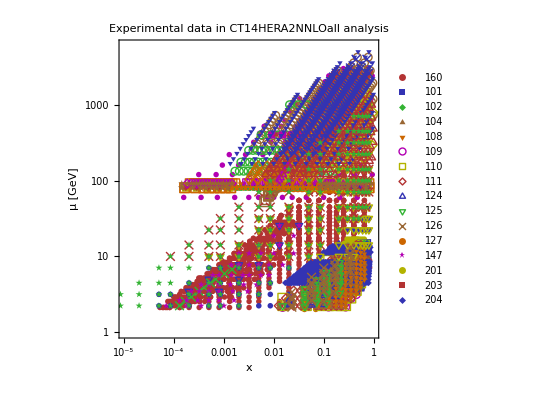

```mathematica
AllexptxQ=
Get["Allexpt_xQbyexpt_xQ-1.m"]
```

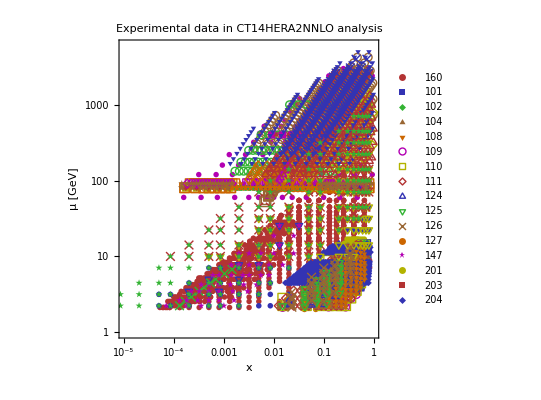

```mathematica
Show[
AllexptxQ,
PlotLabel->Style["Experimental data in CT14HERA2NNLO analysis",24,GrayLevel[0]]
]
```

```mathematica
Export[
"./test/"<>"Allexpt_xQbyexpt_xQ.pdf",
Show[
AllexptxQ,
PlotLabel->Style["Experimental data in CT14HERA2NNLO analysis",24,GrayLevel[0]]
]
]
```

./test/Allexpt_xQbyexpt_xQ.pdf

#### CT14HERA2 LHeC g |sens| xQ

```mathematica
H2LHeCsensxQf0=
Get["H2LHeC_corrdr_plotlist_samept.m"][[0+3,1]]
```

-Graphics-

```mathematica
Show[
H2LHeCsensxQf0,
PlotLabel->Style["|S_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"H2LHeC_corrdr_xQ+1_f0_samept.pdf",
Show[
H2LHeCsensxQf0,
PlotLabel->Style["|S_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->Black
]
]
```

./test/H2LHeC_corrdr_xQ+1_f0_samept.pdf

#### CT14HERA2 LHeC d |sens| xQ

```mathematica
H2LHeCsensxQf2=
Get["H2LHeC_corrdr_plotlist_samept.m"][[2+3,1]]
```

-Graphics-

```mathematica
Show[
H2LHeCsensxQf2,
PlotLabel->Style["|S_f(d(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,GrayLevel[0]},{14,GrayLevel[0]}},
LabelStyle->Black
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"H2LHeC_corrdr_xQ+1_f2_samept.pdf",
Show[
H2LHeCsensxQf2,
PlotLabel->Style["|S_f(g(x,Q), r_i)|, CT14HERA2NNLO",24,GrayLevel[0]],
FrameTicksStyle->{{14,GrayLevel[0]},{14,GrayLevel[0]}},
LabelStyle->Black
]
]
```

./test/H2LHeC_corrdr_xQ+1_f2_samept.pdf